## AntiWindup control (Problem 7.14)

```mathematica
Clear["Global`*"];
```

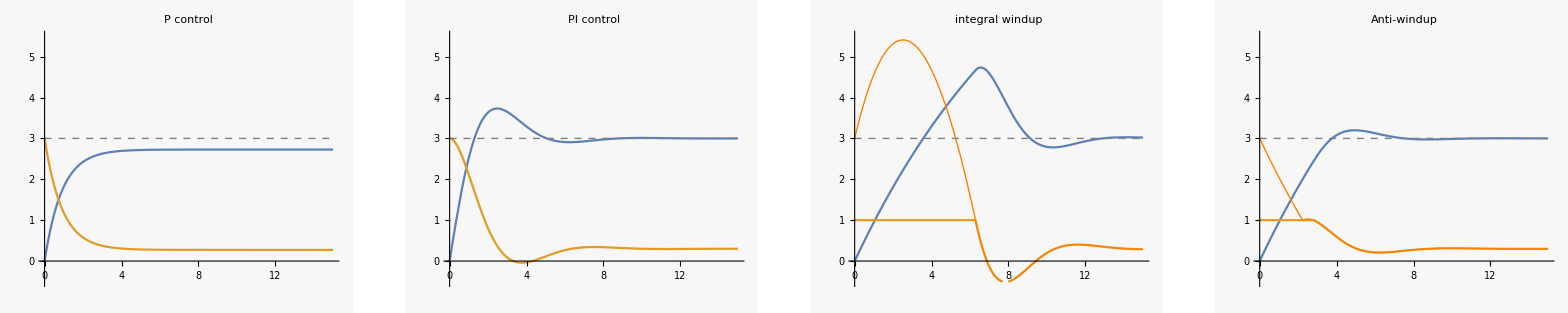

```mathematica
k=1;r=3;τ=15; umax=1;a=0.1;prange={-0.5,5.5};

j0[k_,r_,τ_,a_]:=Module[{eq,init,x,u,t},
eq={x'[t]==-a x[t]+u[t],    u[t]==k(r-x[t])   };
init={x[0]==0};
NDSolveValue[{eq,init},{x,u},{t,0,τ}]]

j1[k_,r_,τ_,a_]:=Module[{eq,init,x,u,t},
eq={x'[t]==-a x[t]+u[t],   u'[t]==-k (-a x[t]+u[t])+k(r-x[t])  };
init={x[0]==0,u[0]==k r};
NDSolveValue[{eq,init},{x,u},{t,0,τ}]]

j2[k_,r_,τ_,umax_,a_]:=Module[{eq,init,x,u,v,t},
eq={x'[t]==-a x[t]+u[t],  u[t]== Clip[v[t],{-umax,umax}],v'[t]==-k (-a x[t]+u[t])+k(r-x[t])};
init={x[0]==0,v[0]==k r};
NDSolveValue[{eq,init},{x,u,v},{t,0,τ}]]

j3[k_,r_,τ_,umax_,a_]:=Module[{eq,init,x,u,v,t},
eq={x'[t]==-a x[t]+u[t],   u[t]== Clip[v[t],{-umax,umax}],
v'[t]==-k (-a x[t]+u[t])+k(r-x[t])UnitStep[umax-v[t]^2]
(* UnitStep turns off integration when |u|>umax *)};
init={x[0]==0,v[0]==k r};
NDSolveValue[{eq,init},{x,u,v},{t,0,τ}]]

{x0,u0}=j0[k,r,τ,a];
{x1,u1}=j1[k,r,τ,a];
{x2,u2,v2}=j2[k,r,τ,umax,a];
{x3,u3,v3}=j3[k,r,τ,umax,a];

p0=Plot[{x0[t],u0[t],r},{t,0,τ},PlotRange->prange,PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotLabel->"P control"];
p1=Plot[{x1[t],u1[t],r},{t,0,τ},PlotRange->prange,PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotLabel->"PI control"];
p2=Plot[{x2[t],u2[t],v2[t],r},{t,0,τ},PlotRange->prange,PlotStyle->{,,Directive[Orange,Thin],Directive[Gray,Dashed,Thin]},PlotLabel->"integral windup"];
p3=Plot[{x3[t],u3[t],v3[t],r},{t,0,τ},PlotRange->prange,PlotStyle->{,,Directive[Orange,Thin],Directive[Gray,Dashed,Thin]},PlotLabel->"Anti-windup"];

GraphicsRow[{p0,p1,p2,p3},Spacings->10,ImageSize->{700}]
```